```mathematica
Print["A skyrmion"]
α=2Pi/3;
b=2ArcTan[Sqrt[u^2+v^2]];
a=ArcTan[u,v]-α;
Print["n=",n={-Sin[a]Sin[b],Cos[a]Sin[b],Cos[b]}]
Print["|n|=",Dot[n,n]//Simplify]
Print["H=",
H=1/2Integrate[(Dot[D[n,u],D[n,u]]+Dot[D[n,v],D[n,v]]),{u,-Infinity,Infinity},{v,-Infinity,Infinity}]]
Print["Q=",
Q=1/(4Pi)Integrate[Dot[n,Cross[D[n,u],D[n,v]]],{u,-Infinity,Infinity},{v,-Infinity,Infinity}]]
n3=ArcCos[n[[3]]];
sc=6;
l=D[n,u].D[n,u]+D[n,v].D[n,v];
```

A skyrmion

n={Cos[π/6-ArcTan[u,v]] Sin[2 ArcTan[√(u^2+v^2)]],-Sin[2 ArcTan[√(u^2+v^2)]] Sin[π/6-ArcTan[u,v]],Cos[2 ArcTan[√(u^2+v^2)]]}

|n|=1

H=4 π

Q=1

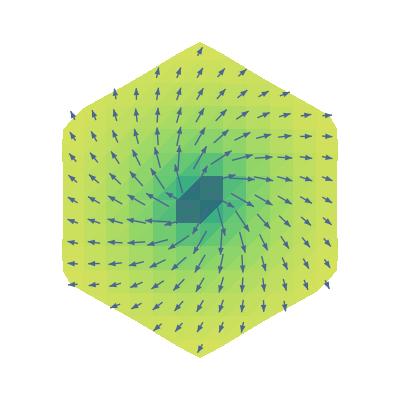

```mathematica
Hexagone=Interpolation[Table[{a,sc*1.06{Cos[a],Sin[a]}},{a,-π,π,π/3}],InterpolationOrder->1];VectorDensityPlot[{Take[n,2],ArcCos[n[[3]]]},{u,-sc,sc},{v,-sc,sc},ColorFunction->"BlueGreenYellow",Frame->False,RegionFunction->Function[{x,y,z},Norm@{x,y}≤Norm@Hexagone[ArcTan[y,x+0.00001]]]]
```

```mathematica
VectorPlot3D[n,{u,-sc,sc},{v,-sc,sc},{w,-1,1},BoxRatios->{1,1,1/sc},RegionFunction->Function[{u,v,w},Norm@{u,v}≤Norm@Hexagone[ArcTan[u,v+0.00001]]&&-0.05<w<0.0000004], VectorPoints->30,VectorStyle->"Arrow3D",VectorScale->0.05,Boxed->False,Axes->False,ImageSize->{90,50},VectorColorFunction->Function[{u,v,w,n1,n2,n3},ColorData["Rainbow"][n3]]]
```

-Graphics3D-